```mathematica
Unprotect[Power];
Power[0,0]=1;
Power[0.,0]=1;
Power[0,0.]=1;
Power[0.,0.]=1;
Protect[Power];
getTransMat[n_] := Table[PDF[BinomialDistribution[2 n, i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen]]][j],
{i,0,2n},{j,0,2n}]
```

```mathematica
popsize=500;
```

```mathematica
getTransMat[popsize]//AbsoluteTiming
```

```mathematica
α=0.01;
Λ=1;
w=1;
vg=0.01;
```

```mathematica
getTransMat[1]
```

{{1.,0.,0.},{(1/2-0.0025 ⅇ^(-0.01 gen))^2,2 (1/2-0.0025 ⅇ^(-0.01 gen)) (1/2+0.0025 ⅇ^(-0.01 gen)),(1/2+0.0025 ⅇ^(-0.01 gen))^2},{0.,0.,1.}}

```mathematica
Flatten[%]
```

{1.,0.,0.,(1/2-0.0025 ⅇ^(-0.01 gen))^2,2 (1/2-0.0025 ⅇ^(-0.01 gen)) (1/2+0.0025 ⅇ^(-0.01 gen)),(1/2+0.0025 ⅇ^(-0.01 gen))^2,0.,0.,1.}

```mathematica
getTransMat[popsize]//AbsoluteTiming
```

```mathematica
getTransMat[n_,gen_] := Table[PDF[BinomialDistribution[2 n, i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen]]][j],
{i,0,2n},{j,0,2n}]
```

```mathematica
getTransMat[popsize,1]//AbsoluteTiming
```

General::munfl: 0.00100989^103 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00100989^104 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00100989^105 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
%37[[2]]
```

```mathematica
Dimensions[%37[[2]]]
```

{1001,1001}

```mathematica
Dimensions[%37[[2]][[2;;2popsize, 2;;2popsize]]]
```

{999,999}

```mathematica
Min[%37[[2]][[2;;2popsize, 2;;2popsize]]]
```

0.

```mathematica
%37[[2]][[2;;2popsize, 2;;2popsize]]<10^-6
```

```mathematica
Clip[%37[[2]],{10^-6,∞},{0,-1}]
```

```mathematica
Min[%]
```

0

```mathematica
Total[Map[Count[0],%%]]
```

889422

```mathematica
Total[Map[Count[0.],%37[[2]]]]
```

547349

```mathematica
1001^2
```

1002001

```mathematica
%%/%
```

49759/91091

```mathematica
%//N
```

0.546256

```mathematica
%37[[2]][[1,2]]
```

0.

```mathematica
Count[%%,0]
```

0

```mathematica
DistributeDefinitions[Power]
```

{}

```mathematica
Unprotect[Power];
Power[0,0]=1;
Power[0.,0]=1;
Power[0,0.]=1;
Power[0.,0.]=1;
Protect[Power];
```

```mathematica
0^i/.i->0
```

1

```mathematica
myPower[x_,y_]:=x^y
myPower[0,0]=1;
myPower[0.,0]=1;
myPower[0,0.]=1;
myPower[0.,0.]=1;
```

```mathematica
testFunction[i_]=Module[
{Power},
Unprotect[Power];
Power=myPower;
Protect[Power];
0
]
```

```mathematica
testFunction[i_]=Module[
{Power},
Unprotect[Power];
Power=myPower;
Protect[Power];
0
]
```

```mathematica
testFunction[i_]=Module[
{Power},
Unprotect[Power];
Power[0,0]=1;
Protect[Power];
0^i];
```

```mathematica
testFunction[0]
```

1

```mathematica
$override=True
Unprotect[Power];
Power[argsandopts___]/;$override==True:=Block[{$override=False},myPower[argsandopts]];
Protect[Power];
```

True

{}

```mathematica
Parallelize;
Parallel`Developer`$InitCode=Hold[Unprotect[Power];Power[0,0]=1;Protect[Power]]
```

Hold[Unprotect[Power];0^0=1;Protect[Power]]

```mathematica
ParallelTable[i^i,{i,{1, 1, 1, 0, 0}}]
```

{1,1,1,1,1}

```mathematica
getTransMat[n_,gen_] := ParallelTable[PDF[BinomialDistribution[2 n, i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen]]][j],
{i,0,2n},{j,0,2n}]
```

```mathematica
PDF[BinomialDistribution[2 n, i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen]]][j]/.{i->0,j->0}
```

Piecewise[{{1, 0≤2 n}, {0, True}}]

```mathematica
Off[General::munfl]
```

```mathematica
getTransMat[popsize,1] //AbsoluteTiming
```

Power::indet: Indeterminate expression 0.^0 encountered.

```mathematica
(*Table[getTransMat[popsize]/.gen->i-1,{i,2}]*)
```

```mathematica
(*Dimensions[%[[1]]]*)
```

{1001,1001}

```mathematica
(*%%[[1]][[1,1]]*)
```

1

```mathematica
/.
```

```mathematica
Unprotect[Power];
Power[0,0]=1;
Power[0.,0]=1;
Power[0,0.]=1;
Power[0.,0.]=1;
Protect[Power];
getTransMat[n_,gen_] := Table[PDF[BinomialDistribution[2 n, i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen]]][j],
{i,0,2n},{j,0,2n}]
```

```mathematica
popsize=50;
α=0.01;
Λ=1;
w=1;
vg=0.01;
```

```mathematica
transMats = Table[getTransMat[popsize,k-1],{k,1,50}]
```

```mathematica
Dimensions[transMats[[1]]]
```

{101,101}

```mathematica
Total[Map[Count[0.],transMats[[1]]]]
```

200

```mathematica
getTransMat[500,0]
```

General::munfl: 0.00100999^103 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00100999^104 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.00100999^105 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Total[Map[Count[0.],%]]
```

547334

```mathematica
transMats[[1]][[1]]
```

{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Total[Map[Count[0.],%]]
```

0

```mathematica
Count[%%,0.]
```

100

```mathematica
longTimeTransMat = Parallelize[Apply[Dot, transMats]];
```

```mathematica
Dimensions[%]
```

{101,101}

```mathematica
init = {ConstantArray[0,2 popsize + 1]}
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
Dimensions[%]
```

{1,101}

```mathematica
popsize / 10 + 1
```

6

```mathematica
init[[1,6]]=1
```

1

```mathematica
init
```

{{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
init.longTimeTransMat
```

{{0.772056,0.00492809,0.00546787,0.00555496,0.00554327,0.00549697,0.00543131,0.00535447,0.00527095,0.00518323,0.0050928,0.00500067,0.00490749,0.00481376,0.00471981,0.00462592,0.0045323,0.00443908,0.00434642,0.00425439,0.00416309,0.00407258,0.00398292,0.00389415,0.00380632,0.00371945,0.00363357,0.00354871,0.00346489,0.00338212,0.00330041,0.00321978,0.00314023,0.00306179,0.00298444,0.00290819,0.00283306,0.00275904,0.00268614,0.00261435,0.00254368,0.00247412,0.00240568,0.00233835,0.00227214,0.00220703,0.00214303,0.00208013,0.00201833,0.00195762,0.001898,0.00183947,0.00178202,0.00172564,0.00167033,0.00161609,0.0015629,0.00151076,0.00145967,0.00140961,0.00136059,0.00131258,0.0012656,0.00121962,0.00117464,0.00113065,0.00108765,0.00104563,0.00100458,0.000964484,0.000925342,0.000887144,0.000849881,0.000813544,0.000778123,0.000743611,0.000709997,0.000677273,0.000645429,0.000614455,0.000584343,0.000555081,0.000526661,0.000499072,0.000472304,0.000446347,0.000421189,0.000396819,0.000373226,0.000350396,0.000328315,0.000306966,0.000286329,0.000266376,0.000247065,0.000228318,0.000209998,0.000191849,0.000172564,0.000143935,0.000671996}}

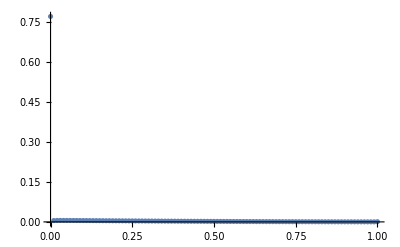

```mathematica
ListPlot[%,DataRange->{0,1}, PlotRange->All]
```

```mathematica
%
```

```mathematica
Parallelize;
Parallel`Developer`$InitCode=Hold[
Unprotect[Power];
Power[0,0]=1;
Power[0.,0]=1;
Power[0,0.]=1;
Power[0.,0.]=1;
Protect[Power]]
ParallelEvaluate[Off[General::munfl]]
```

Hold[Unprotect[Power];0^0=1;0.^0=1;0^0.=1;0.^0.=1;Protect[Power]]

{Null,Null,Null,Null}

```mathematica
popsize=100;
α=0.01;
Λ=1;
w=1;
vg=0.01;
```

```mathematica
getTransMat[n_,gen_] := ParallelTable[PDF[BinomialDistribution[2 n, i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen]]][j],
{i,0,2n},{j,0,2n}]
```

```mathematica
transMat = getTransMat[popsize,1]//AbsoluteTiming
```

```mathematica
myPower[x_,y_]:=x^y
myPower[0,0]=1;
myPower[0.,0]=1;
myPower[0,0.]=1;
myPower[0.,0.]=1;
```

```mathematica
getTest[n_,gen_] := ParallelTable[Binomial[2n,j]myPower[(1-(i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen])),2n-j]myPower[i/(2n) +i/(2n) (1-i/(2n)) (α Λ)/w Exp[-vg/w gen], j],{i,0,2n},{j,0,2n}]
```

```mathematica
test = getTest[popsize,1] //AbsoluteTiming
```

```mathematica
transMat[[2]] == test[[2]]
```

False

```mathematica
Dimensions[test[[2]]-transMat[[2]]]
```

General::munfl: 1.50785×10^-303-1.50784×10^-303 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.73748×10^-297-7.73748×10^-297 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.22955×10^-300-7.22955×10^-300 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{201,201}

```mathematica
Total[Total[test[[2]]-transMat[[2]]]]
```

General::munfl: 1.50785×10^-303-1.50784×10^-303 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.73748×10^-297-7.73748×10^-297 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 7.22955×10^-300-7.22955×10^-300 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

2.88298×10^-16